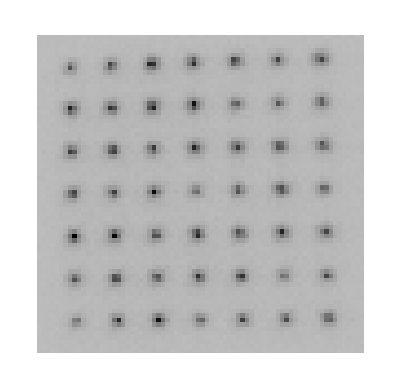

```mathematica
SetDirectory["C:/Users/zhouyu/Desktop/S41"];
filenames=FileNames["*.tga"];


matrixlist=Table[Partition[Import[filenames[[i]],"UnsignedInteger16"][[10;;]],140],{i,1,300}];


avgmatrix=Mean[matrixlist];


croppedmatrixlist=matrixlist[[All,220-99;;220-28,34;;107]];
croppedavgmatrix=avgmatrix[[220-99;;220-28,34;;107]];

ArrayPlot[croppedavgmatrix]
```

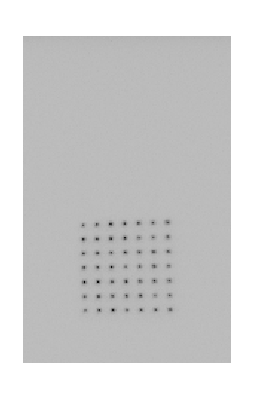

```mathematica
ArrayPlot[avgmatrix]
```

```mathematica
bgnoise=Mean[Flatten[avgmatrix[[220-155;;220-110,32;;77]]]]   (*(32,155)to(77,110)*)
subtravgmatrix=croppedavgmatrix-bgnoise;
ArrayPlot[subtravgmatrix]
```

10452037/25392

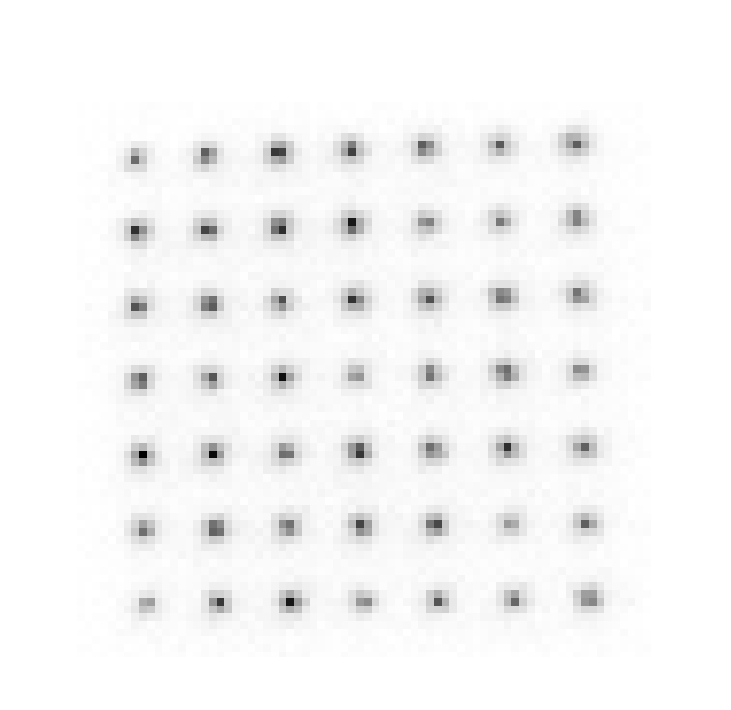

```mathematica
(*MatrixForm[subtravgmatrix]；*)
Dimensions[subtravgmatrix]
```

```mathematica
{72,74}
(*selected atom coordinate (28,7)->region(25-31,4-10)*)

ArrayPlot[subtravgmatrix[[72-10;;72-4,25;;31]]]
```

{72,74}

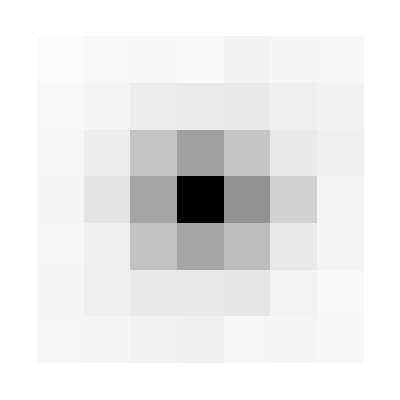

```mathematica
subtrmatrixlist=croppedmatrixlist-bgnoise;
countlist=Table[Total[Flatten[subtrmatrixlist[[i,72-10;;72-4,25;;31]]]],{i,1,300}];
Histogram[countlist,60]
```

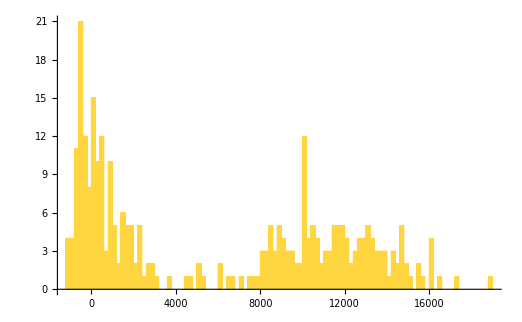
```mathematica
-Graphics-
(*I suggest take 5000 as a threshold *)
```

```mathematica
(*calculating loading rate*)
loadingrate=N[Length[Cases[countlist,_?(#>5000&)]]/Length[countlist]]
```

```mathematica
0.5033333333333333
```

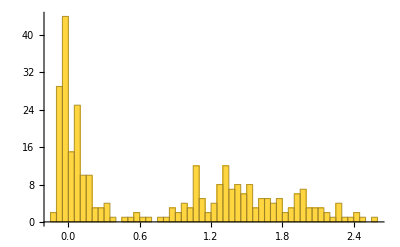

0.51

```mathematica
(*shape function and inner product(weighting)*)
ipcountlist=Table[Total[Flatten[subtrmatrixlist[[i,72-10;;72-4,25;;31]].subtravgmatrix[[72-10;;72-4,25;;31]]]],{i,1,300}];
Histogram[ipcountlist,60]
loadingratemethod2=N[Length[Cases[ipcountlist,_?(#>5000000&)]]/Length[ipcountlist]]
(*set up threshold as 5000000*)
```